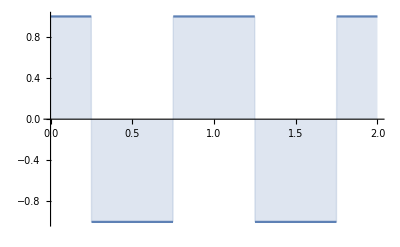

Piecewise[{{-1, 0.25≤x<0.75||1.25≤x<1.75}, {1, True}}]

0.

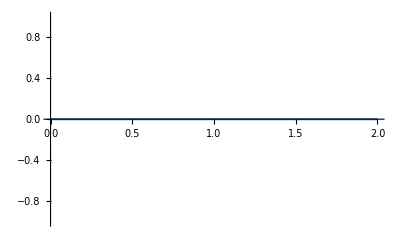

Piecewise[{{1/4 (-9-8 x-8 x^2), -3/4<x≤-1/4}, {1/4 (-9+8 x-8 x^2), 1/4<x≤3/4}, {2 (-1+x^2), -1/4<x≤1/4}, {2 (-2 x+x^2), x>3/4}, {2 (2 x+x^2), True}}]

```mathematica
ClearAll[f]


f[x_]:=SquareWave[x+0.25]
Plot[f[x],{x,0,2},Filling->Axis]

PiecewiseExpand[f[x],0≤x≤2 ]
PiecewiseExpand[Integrate[f[x],{x,0,2} ],0≤x≤2 ]

Plot[%,{x,0,2},PlotRange->All]
```

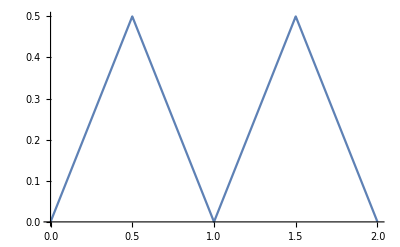

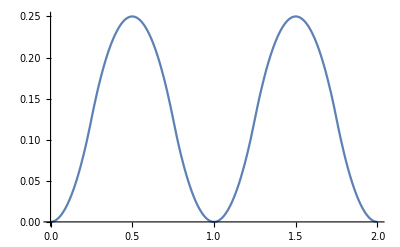

```mathematica
Plot[Integrate[SquareWave[x],{x,0,k}],{k,0,2}]
```

Piecewise[{{-1, 1/2≤x<1||3/2≤x<2}, {1, True}}]

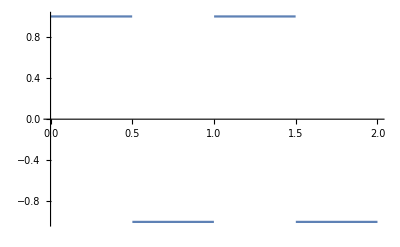

∫_0^b SquareWave[x]ⅆx

Integrate[SquareWave[x],{x,0,b},Assumptions→0≤x≤2]

-Graphics-

∫_0^c (∫_0^b SquareWave[x]ⅆx)[x]ⅆx

Integrate[Integrate[SquareWave[x],{x,0,b},Assumptions→0≤x≤2][x],{x,0,c},Assumptions→0≤x≤2]

NIntegrate::inumr: The integrand (∫_0^b SquareWave[x]ⅆx)[x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1325531411/32443076493007}}.

NIntegrate::nlim: x = b is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::inumr: The integrand NIntegrate[SquareWave[x],{x,0,b}][x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1325531411/32443076493007}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
ClearAll[f,x,k,g,h,b,c,a]
f[x_]:=SquareWave[x];
PiecewiseExpand[f[x],0<=x<=2]
Plot[f[a],{a,0,2}]

g=Integrate[f[x],{x,0,b}]
PiecewiseExpand[g,0<=x<=2]
Plot[g,{b,0,2}]

h=Integrate[g,{x,0,c}]
PiecewiseExpand[h,0<=x<=2]
Plot[h,{c,0,2}]
```

```mathematica
Integrate[f[x],{x,0,b}]
```

∫_0^b SquareWave[x]ⅆx